This notebook requires the library Melt (https://melt1.notion.site). To load the library simply run the cell below. 
If that does not work, open the other Mathematica notebook entitled Melt.nb, then go to Evaluation → Evaluate Initialization Cells. 
This will load up all functions in Melt.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
LoadPauliMatrices[]
LoadPlotStyling[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

## PRX Quantum tutorial - Examples

## Example A

### Steady-state and average current

```mathematica
Clear[Δ,Ω,γ,n];
H = Δ/2 σz + Ω σx;
cops = {σm,σp};
rates = {γ (n+1),γ n};
ccops = √rates cops;
ℒ = Liouvillian[H,cops,rates];
ρ = AnalyticalSteadyState[ℒ]//cf//mf;
```

((n ((γ+2 n γ)^2+4 Δ^2)+4 (1+2 n) Ω^2)/((1+2 n) ((γ+2 n γ)^2+4 (Δ^2+2 Ω^2))) | -(2 ⅈ (γ+2 n γ-2 ⅈ Δ) Ω)/((1+2 n) ((γ+2 n γ)^2+4 (Δ^2+2 Ω^2)))
(2 ⅈ (γ+2 n γ+2 ⅈ Δ) Ω)/((1+2 n) ((γ+2 n γ)^2+4 (Δ^2+2 Ω^2))) | ((1+n) ((γ+2 n γ)^2+4 Δ^2)+4 (1+2 n) Ω^2)/((1+2 n) ((γ+2 n γ)^2+4 (Δ^2+2 Ω^2))))

```mathematica
(* Average particle current *)
J=FCSAverage[ρ,ℒ,ccops,{-1,1}]//cf
```

-(4 γ Ω^2)/((γ+2 n γ)^2+4 (Δ^2+2 Ω^2))

```mathematica
γ n Tr[σm.σp.ρ] - γ (n+1) Tr[σp.σm.ρ]//cf
```

-(4 γ Ω^2)/((γ+2 n γ)^2+4 (Δ^2+2 Ω^2))

```mathematica
(* Dynamical activity - Subscript[ν, 1]=Subscript[ν, 2]=1 *)
FCSAverage[ρ,ℒ,√rates cops,{1,1}]//cf
%/.Ω->0
```

(2 n (1+n) γ ((γ+2 n γ)^2+4 Δ^2)+4 γ (Ω+2 n Ω)^2)/((1+2 n) ((γ+2 n γ)^2+4 (Δ^2+2 Ω^2)))

(2 n (1+n) γ)/(1+2 n)

### F(τ), g^(2), S(ω) and D

```mathematica
H =  Ω σx;
c = √γ σm;
ℒ = Liouvillian[H,c]//cf//mf;
ρ = AnalyticalSteadyState[ℒ]//cf//mf;
```

(-γ | -ⅈ Ω | ⅈ Ω | 0
-ⅈ Ω | -γ/2 | 0 | ⅈ Ω
ⅈ Ω | 0 | -γ/2 | -ⅈ Ω
γ | ⅈ Ω | -ⅈ Ω | 0)

((4 Ω^2)/(γ^2+8 Ω^2) | -(2 ⅈ γ Ω)/(γ^2+8 Ω^2)
(2 ⅈ γ Ω)/(γ^2+8 Ω^2) | (γ^2+4 Ω^2)/(γ^2+8 Ω^2))

```mathematica
J = FCSAverage[ρ,ℒ,√rates cops]//cf
```

(4 γ Ω^2)/(γ^2+8 Ω^2)

```mathematica
F=FCSTwoPointFunction[t,ρ,ℒ,√rates cops]//cf
```

-(16 ⅇ^(-(3 t γ)/4) γ^2 Ω^4 (√(γ^2-64 Ω^2) Cosh[1/4 t √(γ^2-64 Ω^2)]+3 γ Sinh[1/4 t √(γ^2-64 Ω^2)]))/(√(γ^2-64 Ω^2) (γ^2+8 Ω^2)^2)

```mathematica
g2=F/J^2+1//cf
g2/.t->0//cf
g2-FCSg2[t,ρ,ℒ,√γ σm]//cf
```

1+ⅇ^(-(3 t γ)/4) (-Cosh[1/4 t √(γ^2-64 Ω^2)]-(3 γ Sinh[1/4 t √(γ^2-64 Ω^2)])/(√(γ^2-64 Ω^2)))

0

0

```mathematica
S = FCSPowerSpectrum[ω,ρ,ℒ,c]//cf
```

(4 γ Ω^2 (γ^4+γ^2 (5 ω^2-8 Ω^2)+4 (ω^2-4 Ω^2)^2))/((γ^2+8 Ω^2) (γ^4+4 (ω^2-4 Ω^2)^2+γ^2 (5 ω^2+16 Ω^2)))

```mathematica
𝒟 = FCSNoise[ρ,ℒ,c]//cf
```

(4 γ Ω^2 (γ^4-8 γ^2 Ω^2+64 Ω^4))/((γ^2+8 Ω^2)^3)

### Emission/absorption spectra and g^(1)

```mathematica
(* Define Hamiltonian and Liouvillian *)
```

```mathematica
H =  Δ σz/2+Ω σx;
c = {√(γ(1+n))σm,√(γ n)σp};
ℒ = Liouvillian[H,c]//cf;
ρ = AnalyticalSteadyState[ℒ]//cf;
```

```mathematica
(* Compute emission and absorption spectrum for two different parameters *)
ws = Range[-3.5,3.5,0.0011];
params1 = {Ω->1,γ->0.2,Δ->0,n->0.1};
params2 = {Ω->1,γ->2,Δ->0,n->0.1};
E1=EmissionSpectrum[ρ/.params1,ws,ℒ/.params1,Sqrt[γ]σm/.params1]/(2Pi);
E2=EmissionSpectrum[ρ/.params2,ws,ℒ/.params2,Sqrt[γ]σm/.params2]/(2Pi);
A1=EmissionSpectrum[ρ/.params1,ws,ℒ/.params1,Sqrt[γ]σp/.params1]/(2Pi);
A2=EmissionSpectrum[ρ/.params2,ws,ℒ/.params2,Sqrt[γ]σp/.params2]/(2Pi);
```

```mathematica
COLORLIST
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]}

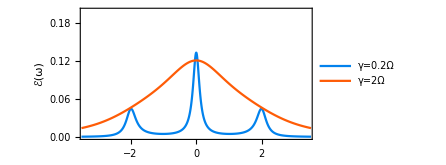

```mathematica
(* Emission spectrum *)
emplot=ListLinePlot[{Partition[Riffle[ws,E1],2],Partition[Riffle[ws,E2],2]},PlotRange->{{-3.4,3.4},{0,0.2}},PlotStyle->{COLORLIST⟦4⟧,COLORLIST⟦2⟧},FrameLabel->{"(ω-ω_d)/Ω","ℰ(ω)"},AspectRatio->0.5, PlotLegends->legend[{"γ=0.2Ω","γ=2Ω"},{0.8,0.72},LegendLayout->"Column"]]
```

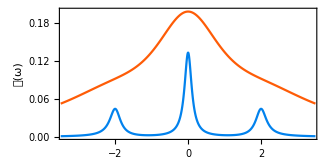

```mathematica
(* Incoherent absorption spectrum *)
incplot=ListLinePlot[{Partition[Riffle[ws,A1],2],Partition[Riffle[ws,A2],2]},PlotRange->{{-3.4,3.4},{0,0.2}},PlotStyle->{COLORLIST⟦4⟧,COLORLIST⟦2⟧},
FrameLabel->{"(ω-ω_d)/Ω","𝒜(ω)"},AspectRatio->0.5]
```

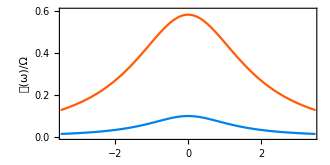

```mathematica
(* Coherent absorption spectrum *)
W[w_]:=(Ω Tr[σy.ρ])/.Δ->w
cohplot=Plot[{W[w]/.params1,W[w]/.params2},{w,-3.5,3.5},FrameLabel->{"(ω_d-ω_0)/Ω","𝒲(ω)/Ω"},PlotRange->{{-3.4,3.4},{0,0.6}},PlotStyle->{COLORLIST⟦4⟧,COLORLIST⟦2⟧},AspectRatio->0.5]
```

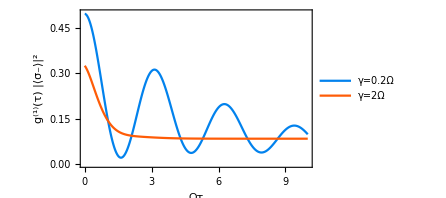

```mathematica
(* Compute g^(1) for those parameters *)
tlist = Range[0,10,0.01];
g11=FCSCorr[tlist,ρ/.params1,ℒ/.params1,σ0,σp,σm];
g12=FCSCorr[tlist,ρ/.params2,ℒ/.params2,σ0,σp,σm];

g1plot=ListLinePlot[{g11,g12},PlotRange->{{0,10},{0,0.5}},
FrameLabel->{"Ωτ",Style["g^(1)(τ) |⟨σ_-⟩|^2",Italic]},PlotLegends->legend[{"γ=0.2Ω","γ=2Ω"},{0.8,0.76},LegendLayout->"Column"],PlotStyle->{COLORLIST⟦4⟧,COLORLIST⟦2⟧},
AspectRatio->0.6
]
```

### FCS full probability distribution - quantum jumps

```mathematica
Δ = 0;
Ω = γt = 1.0;
Nb = 0.2;
H = Ω σx;
cops = {√(γt(Nb+1))σm, √(γt Nb)σp};
ℒ = Liouvillian[H,cops];
ρ = SteadyState[ℒ]//mf;
```

(0.429719 | 0.-0.200803 ⅈ
0.+0.200803 ⅈ | 0.570281)

```mathematica
ts = {5,15,30,50};
do[
P[t] = FCSProbability[t,ρ,ℒ,cops,{-1,1}],
{t,ts}]
```

0h : 0m : 0s

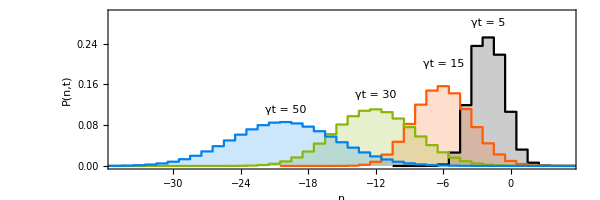

```mathematica
ListStepPlot[Table[P[t],{t,ts}],Center,Filling->Axis,
PlotRange->{{-35,5},{0,0.3}},
AspectRatio->1/3,
ImageSize->600,
Frame->True,
Axes->None,
PlotStyle->COLORLIST,
BaseStyle->{FontFamily->"Times",24},
PlotRangePadding->{{None,None},{None,Scaled[0.1]}},
FrameLabel->{Style["n",Italic],Style["P(n,t)",Italic]},
Epilog->{
Text["γt = 5",{-2,0.28}],
Text["γt = 15  ",{-6,0.2}],
Text["γt = 30",{-12,0.14}],
Text["γt = 50",{-20,0.11}]
}
]
```

### FCS Full distribution using jump-resolved Kraus operators

```mathematica
Δ = 0;
Ω = γt = 1.0;
Nb = 0.2;
H = Ω σx;
cops = {√(γt(Nb+1))σm, √(γt Nb)σp};
ℒ = Liouvillian[H,cops];
ρss = SteadyState[ℒ]//mf;
He = H - ⅈ/2 Sum[L†.L,{L,cops}];

Clear[M];
dt = 0.001;
M[0] = σ0-ⅈ dt He;
M[1] = √dt cops[[1]];
M[2] = √dt cops[[2]];
ν = {-1,1};
```

(0.429719 | 0.-0.200803 ⅈ
0.+0.200803 ⅈ | 0.570281)

```mathematica
Clear[ρ,P];
nmin = -40;
nmax = +10;
Do[ρ[n] = ConstantArray[0.,Dimensions@ρss],{n,nmin-2,nmax+2}]
ρ[0] = ρss;

Do[
Do[ρ[n] = M[0].ρ[n].M[0]† + M[1].ρ[n-ν[[1]]].M[1]† + M[2].ρ[n-ν[[2]]].M[2]†,{n,nmin,nmax}];

P[t] = Chop@Table[{n,Tr[ρ[n]]},{n,nmin,nmax}];
,{t,0,50,dt}
]
```

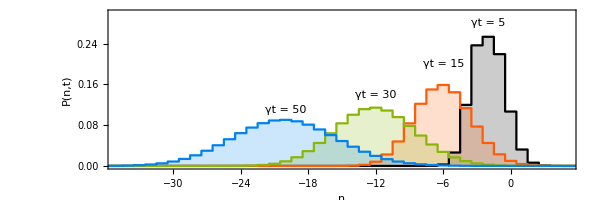

-Graphics-

```mathematica
ts = {5.,15.,30.,50.};
ListStepPlot[Table[P[t],{t,ts}],Center,Filling->Axis,
PlotRange->{{-35,5},{0,0.3}},
AspectRatio->1/3,
PlotRange->All,
ImageSize->600,
Frame->True,
Axes->None,
PlotStyle->COLORLIST,
BaseStyle->{FontFamily->"Times",24},
PlotRangePadding->{{None,None},{None,Scaled[0.1]}},
FrameLabel->{Style["n",Italic],Style["P(n,t)",Italic]},
Epilog->{
Text["γt = 5",{-2,0.28}],
Text["γt = 15  ",{-6,0.2}],
Text["γt = 30",{-12,0.14}],
Text["γt = 50",{-20,0.11}]
}
]
```

### Gammelmark-Mølmer Fisher information

```mathematica
Clear[Ω,Δ,γ]
H = Ω σx;
ℒ = Liouvillian[H,{σm},{γ}];
ρ = SteadyState[ℒ]//cf//mf;
```

((4 Ω^2)/(γ^2+8 Ω^2) | -(2 ⅈ γ Ω)/(γ^2+8 Ω^2)
(2 ⅈ γ Ω)/(γ^2+8 Ω^2) | (γ^2+4 Ω^2)/(γ^2+8 Ω^2))

```mathematica
ℱ=GammelmarkMolmerMFisher[ρ,ℒ,H,σx,{√γ σm},{0 σm}]//cf
```

16/γ

```mathematica
ℱ/.Δ->0//cf
```

16/γ

```mathematica
ℒp=DrazinInverse[ℒ]/.Δ->0//cf//mf;
```

(-(γ (γ^2-4 Ω^2))/((γ^2+8 Ω^2)^2) | (2 ⅈ Ω)/(γ^2+8 Ω^2) | -(2 ⅈ Ω)/(γ^2+8 Ω^2) | (12 γ Ω^2)/((γ^2+8 Ω^2)^2)
(8 ⅈ Ω (γ^2+2 Ω^2))/((γ^2+8 Ω^2)^2) | -1/γ-γ/(γ^2+8 Ω^2) | -(8 Ω^2)/(γ^3+8 γ Ω^2) | (4 ⅈ Ω (γ^2-4 Ω^2))/((γ^2+8 Ω^2)^2)
-(8 ⅈ Ω (γ^2+2 Ω^2))/((γ^2+8 Ω^2)^2) | -(8 Ω^2)/(γ^3+8 γ Ω^2) | -1/γ-γ/(γ^2+8 Ω^2) | -(4 ⅈ Ω (γ^2-4 Ω^2))/((γ^2+8 Ω^2)^2)
(γ (γ^2-4 Ω^2))/((γ^2+8 Ω^2)^2) | -(2 ⅈ Ω)/(γ^2+8 Ω^2) | (2 ⅈ Ω)/(γ^2+8 Ω^2) | -(12 γ Ω^2)/((γ^2+8 Ω^2)^2))

```mathematica
ρ.σx+σx.ρ//cf//mf;
ℒp.Vec[%]//Unvec//cf//mf;
Tr[σx.%]//cf
```

(0 | 1
1 | 0)

(0 | -2/γ
-2/γ | 0)

-4/γ

```mathematica
ℒ//mf;
```

(-γ | -ⅈ Ω | ⅈ Ω | 0
-ⅈ Ω | -γ/2 | 0 | ⅈ Ω
ⅈ Ω | 0 | -γ/2 | -ⅈ Ω
γ | ⅈ Ω | -ⅈ Ω | 0)

```mathematica
GammelmarkMolmerMFisher[ρ,ℒ,H,0σx,{√γ σm},{1/(2 √γ)σm}]//cf
```

(4 Ω^2)/(γ^3+8 γ Ω^2)

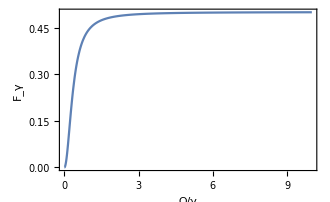

```mathematica
Plot[(4 Ω^2)/(γ^3+8 γ Ω^2)/.γ->1,{Ω,0,10},
FrameLabel->{"Ω/γ","F_γ"}]
```

```mathematica
Limit[(4 Ω^2)/(γ^3+8 γ Ω^2),Ω->∞]
```

1/(2 γ)

## Example B

### Steady-state and average current

```mathematica
Clear[Δ,Ω,γ,n];
H = ω σp.σm;
cops = {σm,σp,σm,σp};
rates = {γL (1-fL),γL fL, γR (1-fR),γR fR};
cs = √rates cops;
ℒ = Liouvillian[H,cops,rates];
ρ = AnalyticalSteadyState[ℒ]//cf//mf;
```

((fL γL+fR γR)/(γL+γR) | 0
0 | (γL-fL γL+γR-fR γR)/(γL+γR))

```mathematica
assumptions = {γL>0,γR>0,0<fL<1,0<fR<1};
```

```mathematica
J = FullSimplify[FCSAverage[ρ,ℒ,cs,{-1,1,0,0}],assumptions]
```

((fL-fR) γL γR)/(γL+γR)

### F, S and D

```mathematica
F = FullSimplify[FCSTwoPointFunction[t,ρ,ℒ,cs,{-1,1,0,0}],assumptions]
```

(ⅇ^(-t (γL+γR)) γL^2 ((-1+fL) fL γL^2+2 (-1+fL) fL γL γR-(fL-2 fL fR+fR^2) γR^2))/(γL+γR)^2

```mathematica
𝒮 = FullSimplify[FCSPowerSpectrum[ω,ρ,ℒ,cs,{-1,1,0,0}],assumptions]
```

(γL γR ((fL+fR-2 fL fR) γL^2+2 (fL-fL^2+fR-fR^2) γL γR+(fL+fR-2 fL fR) γR^2)+γL (-2 fL^2 γL+fR γR+fL (2 γL+γR-2 fR γR)) ω^2)/((γL+γR)^3+(γL+γR) ω^2)

```mathematica
𝒟=FullSimplify[FCSNoise[ρ,ℒ,cs,{-1,1,0,0}],assumptions]
```

(γL γR ((fL+fR-2 fL fR) γL^2+2 (fL-fL^2+fR-fR^2) γL γR+(fL+fR-2 fL fR) γR^2))/(γL+γR)^3

```mathematica
𝒟/.{γL->γ,γR->γ}//cf
```

-1/4 (-2+fL+fR) (fL+fR) γ

### SCGF

```mathematica
Clear[Δ,Ω,γ,n];
H = ω σp.σm;
cops = {σm,σp,σm,σp};
(*rates = {γL fLb,γL fL, γR  fRb,γR fR};*)
rates = {γL (1-fL),γL fL, γR (1-fR),γR fR};
cs = √rates cops;
ℒ = Liouvillian[H,cops,rates];
ρ = AnalyticalSteadyState[ℒ]//cf//mf;
```

((fL γL+fR γR)/(γL+γR) | 0
0 | (γL-fL γL+γR-fR γR)/(γL+γR))

```mathematica
ℒχ = ℒ + (ⅇ^(-ⅈ χ)-1)γL (1-fL)  JumpOp[σm]+(ⅇ^(ⅈ χ)-1)γL fL  JumpOp[σp];
```

```mathematica
Eigenvalues[ℒχ]//cf
```

{1/2 (-γL-γR-ⅇ^(-ⅈ χ) √(ⅇ^(2 ⅈ χ) (γL^2+2 (-1+2 fL) (-1+2 fR) γL γR+γR^2+4 (fL+fR-2 fL fR) γL γR Cos[χ]+4 ⅈ (fL-fR) γL γR Sin[χ]))),1/2 ⅇ^(-ⅈ χ) (-ⅇ^(ⅈ χ) (γL+γR)+√(ⅇ^(2 ⅈ χ) (γL^2+2 (-1+2 fL) (-1+2 fR) γL γR+γR^2+4 (fL+fR-2 fL fR) γL γR Cos[χ]+4 ⅈ (fL-fR) γL γR Sin[χ]))),1/2 (-γL-γR+2 ⅈ ω),1/2 (-γL-γR-2 ⅈ ω)}

### QPC

Add a new jump operator 𝒯 + χ c†c

```mathematica
Clear[Δ,Ω,γ,n];
H = ω σp.σm;
cops = {σm,σp,σm,σp,𝒯 σ0+χ σp.σm};
rates = {γL (1-fL),γL fL, γR (1-fR),γR fR,1};
cs = √rates cops;
ℒ = Liouvillian[H,cops,rates];
ρ = AnalyticalSteadyState[ℒ]//cf//mf;
```

((fL γL+fR γR)/(γL+γR) | 0
0 | (γL-fL γL+γR-fR γR)/(γL+γR))

#### Jump case

```mathematica
cdc=Tr[σp.σm.ρ]//cf
```

(fL γL+fR γR)/(γL+γR)

```mathematica
rep = {𝒯->√𝒫,χ->√𝒫p-√𝒫};
simp = {0<fL<1,0<fR<1,γL>0,γR>0,𝒯>0,χ<0};
```

```mathematica
FullSimplify[FCSAverage[ρ,ℒ,cs,{0,0,1,-1,0}],simp]
```

((fL-fR) γL γR)/(γL+γR)

```mathematica
FCSAverage[ρ,ℒ,cs,{0,0,0,0,1}]//cf
%/.{fL γL + fR γR ->(γL+γR) nb}//cf
Jqpc=%/.rep//cf
```

(𝒯^2 (γL+γR)+2 𝒯 (fL γL+fR γR) χ+(fL γL+fR γR) χ^2)/(γL+γR)

𝒯^2+2 nb 𝒯 χ+nb χ^2

𝒫-nb 𝒫+nb 𝒫p

```mathematica
FullSimplify[FCSTwoPointFunction[t,ρ,ℒ,cs,{0,0,1,-1,0}],simp]
```

(ⅇ^(-t (γL+γR)) γR^2 (-((fL^2+fR-2 fL fR) γL^2)+2 (-1+fR) fR γL γR+(-1+fR) fR γR^2))/(γL+γR)^2

```mathematica
FCSTwoPointFunction[t,ρ,ℒ,cs,{0,0,0,0,1}]//cf
F1=%/.rep//cf
```

-(ⅇ^(-t (γL+γR)) ((-1+fL) γL+(-1+fR) γR) (fL γL+fR γR) χ^2 (2 𝒯+χ)^2)/(γL+γR)^2

-(ⅇ^(-t (γL+γR)) (𝒫-𝒫p)^2 ((-1+fL) γL+(-1+fR) γR) (fL γL+fR γR))/(γL+γR)^2

```mathematica
F2 = ⅇ^(-t (γL+γR)) (𝒫-𝒫p)^2 cdc(1-cdc);
F1-F2//cf
```

0

```mathematica
Integrate[(ⅇ^(ⅈ ω τ)+ⅇ^(-ⅈ ω τ))ⅇ^(-γ τ),{τ,0,∞},Assumptions->{γ>0,ω>0}]
```

(2 γ)/(γ^2+ω^2)

```mathematica
FCSPowerSpectrum[ω,ρ,ℒ,cs,{0,0,0,0,1}]//cf
%/.rep//cf
```

1/((γL+γR)^3+(γL+γR) ω^2)(-((fL γL+fR γR) χ^2 (-(γL+γR)^2+2 ((-1+fL) γL+(-1+fR) γR) χ^2-ω^2))-2 𝒯 (fL γL+fR γR) χ (-(γL+γR)^2+4 ((-1+fL) γL+(-1+fR) γR) χ^2-ω^2)+𝒯^2 (γL^3+γL^2 (3 γR-8 (-1+fL) fL χ^2)+γR (γR (γR-8 (-1+fR) fR χ^2)+ω^2)+γL (γR (3 γR+8 (fL+fR-2 fL fR) χ^2)+ω^2)))

1/((γL+γR)^3+(γL+γR) ω^2)(-2 fL^2 (𝒫-𝒫p)^2 γL^2+2 fR 𝒫^2 γR (γL+γR-fR γR)+fL (𝒫-𝒫p) γL (-(γL+γR)^2+2 𝒫 (γL+γR-2 fR γR)-2 𝒫p (γL+γR-2 fR γR)-ω^2)+𝒫 (γL+γR-fR γR) (-4 fR 𝒫p γR+(γL+γR)^2+ω^2)+fR 𝒫p γR ((γL+γR)^2+2 𝒫p (γL+γR-fR γR)+ω^2))

```mathematica
FCSNoise[ρ,ℒ,cs,{0,0,0,0,1}]//cf
D1=%/.rep//cf
```

(𝒯^2 (γL-fL γL+γR-fR γR)+(fL γL+fR γR) (𝒯+χ)^2+(2 𝒯^2 ((-1+fL) γL+(-1+fR) γR) (fL γL+fR γR) χ (2 𝒯+χ))/(γL+γR)^2-(2 ((-1+fL) γL+(-1+fR) γR) (fL γL+fR γR) χ (𝒯+χ)^2 (2 𝒯+χ))/(γL+γR)^2)/(γL+γR)

-(2 𝒫^2 ((-1+fL) γL+(-1+fR) γR) (fL γL+fR γR)+𝒫 ((-1+fL) γL+(-1+fR) γR) (-4 fL 𝒫p γL-4 fR 𝒫p γR+(γL+γR)^2)+𝒫p (fL γL+fR γR) (-(γL+γR)^2+2 𝒫p ((-1+fL) γL+(-1+fR) γR)))/(γL+γR)^3

```mathematica
D2 = Jqpc + (𝒫p-𝒫)^2 nb(1-nb)2/(γL + γR)/.nb->cdc;
D1-D2//cf
```

0

#### Diffusive case

```mathematica
cops = {σm,σp,σm,σp, χ σp.σm};
rates = {γL (1-fL),γL fL,γR (1-fR),γR fR,1};
ccops = √rates cops;
ℒ = Liouvillian[0 σz,cops,rates];
ρ = SteadyState[ℒ]//cf//mf;
```

((fL γL+fR γR)/(γL+γR) | 0
0 | (γL-fL γL+γR-fR γR)/(γL+γR))

```mathematica
FCSTwoPointFunction[t,ρ,ℒ,ccops,{0,0,0,0,1},"diffusion"]//cf
```

-(4 ⅇ^(-t (γL+γR)) ((-1+fL) γL+(-1+fR) γR) (fL γL+fR γR) χ^2)/(γL+γR)^2

#### Stochastic simulations

```mathematica
makeCurrent[ts_,jumpList_,jumpType_:"all"]:=Module[{jumpTimes,curr},

jumpTimes = If[jumpType==="all",
jumpList[[All,1]],
Select[jumpList,#[[2]]==jumpType&][[All,1]]];

curr = ConstantArray[0,Length@ts];
Do[curr[[j]]=1,{j,jumpTimes}];
{ts,curr}ᵀ

]
```

```mathematica
γL = 0;
γR = 2;
TL = 2.; 
TR = 1.;
ω = 21;
μR = 20.;
μL = 10.;
fL = 1/(ⅇ^((ω-μL)/TL)+1);
fR = 1/(ⅇ^((ω-μR)/TR)+1);

𝒯 = 5.;
χ = 2.9;
cops = {σm,σp,σm,σp,𝒯 σ0 + χ σp.σm};
rates = {γL (1-fL),γL fL,γR (1-fR),γR fR,1};
ccops = (√rates cops)[[{5}]];
sops = (√rates cops)[[1;;4]];

ℒ = Liouvillian[0 σz,cops,rates];
ρ = SteadyState[ℒ]//cf;

ts = Range[0,50,0.001];

{ψ,jumpList}=QuantumJumpUnravelling[0σz,√rates cops,{1,0},ts];
jumpBath=Select[jumpList,#[[2]]==3||#[[2]]==4&];
```

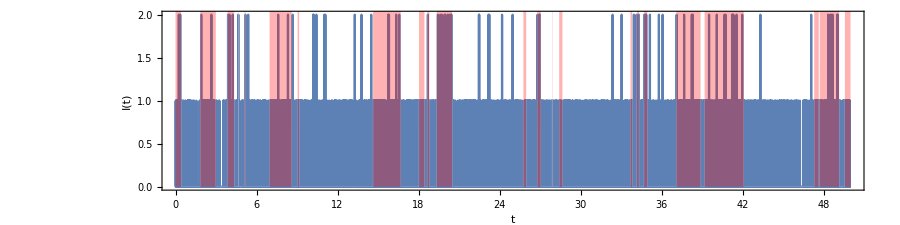

```mathematica
ma = 3;
curr=makeCurrent[ts,jumpList,5];
Show[
ListLinePlot[{#[[1]],ma #[[2]]}&/@MovingAverage[curr,ma]
(*{ts,ma MovingAverage[curr[[All,2]],ma]}ᵀ*),InterpolationOrder->0],
ListLinePlot[{ts,ma Abs[ψ⟦All,1⟧]^2}ᵀ,
PlotStyle->Directive[White,Thickness[0]],
Filling->Axis,FillingStyle->Directive[Red,Opacity[0.3]]
],
AspectRatio->1/4,
ImageSize->900,
FrameLabel->{"t","I(t)"}
]
```

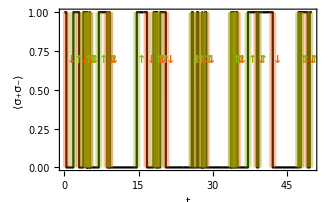

```mathematica
ListLinePlot[{ts,Abs[ψ⟦All,1⟧]^2}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[
jumpBath,
ts,{"↓","↑"}],
FrameLabel->{Style["t",Italic],"⟨σ_+σ_-⟩"}
]
```

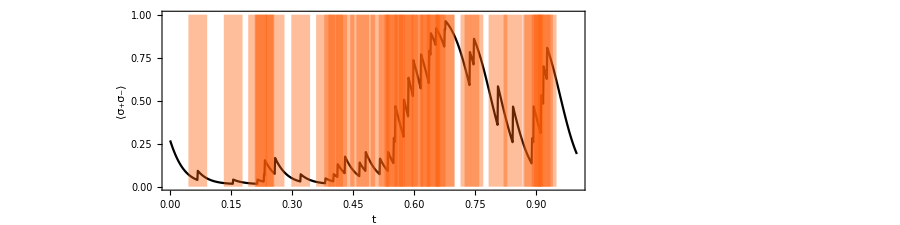

```mathematica
{ρs,jumpList}=QuantumJumpUnravellingMixedStates[0σz, ccops,sops,ρ,Range[0,1,0.001]];
ListLinePlot[{Range[0,1,0.001],Table[Tr[r.σp.σm],{r,ρs}]}ᵀ,
PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↑"}],
FrameLabel->{Style["t",Italic],"⟨σ_+σ_-⟩"},
PlotRange->{0,1},
AspectRatio->1/4,
ImageSize->900
]
```

## Example C

### Steady-state

```mathematica
Clear[Δ,Ω,Γ];
Δ = 0;
H = Δ/2 σz + Ω σx;
c = √Γ σz;
ℒ = Liouvillian[H,{σz},{Γ}];
ρ = SteadyState[ℒ]//mf;
```

(1/2 | 0
0 | 1/2)

```mathematica
Eigenvalues[ℒ]
```

{0,-2 Γ,-Γ-√(Γ^2-4 Ω^2),-Γ+√(Γ^2-4 Ω^2)}

### F, S and D

```mathematica
F=FCSTwoPointFunction[t,ρ,ℒ,c,1,"diffusion"]//cf
```

4 ⅇ^(-t Γ) Γ (Cosh[t √(Γ^2-4 Ω^2)]+(Γ Sinh[t √(Γ^2-4 Ω^2)])/(√(Γ^2-4 Ω^2)))

```mathematica
S=FCSPowerSpectrum[ω,ρ,ℒ,c,1,"diffusion"]//cf
```

1+(64 Γ^2 Ω^2)/(4 Γ^2 ω^2+(ω^2-4 Ω^2)^2)

```mathematica
𝒟 = FCSNoise[ρ,ℒ,c,1,"diffusion"]//cf
```

1+(4 Γ^2)/Ω^2

### FCS full probability distribution - quantum diffusion

```mathematica
Clear[P,p,ts,Δ,Ω,H,κs,L,ℒ,ρ];

ts = {0.1,0.2,0.5,1.0,2.0,3.0,5.0};
Δ = 0.0;
Ω = 1.0;
H = Δ/2 σz+σx;
κs = {0.2,1.0,2.0};
Clear[κ];
Do[
L = √κ σz;
ℒ = Liouvillian[H,{L}];
ρ = SteadyState[ℒ];
do[
P[t,κ] = FCSProbabilityDiffusion[t,ρ,ℒ,L,10,1000];
p[t,κ]=Table[{n,P[t,κ][n]},{n,-20,20,0.025}];
norm = (p[t,κ]⟦All,2⟧)//Total;
p[t,κ] ={#⟦1⟧,#⟦2⟧/norm}&/@ p[t,κ];

,{t,ts}];
,{κ,κs}]
```

0h : 0m : 3s

0h : 0m : 2s

0h : 0m : 2s

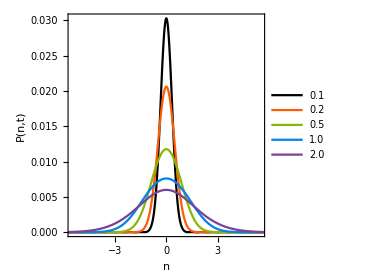
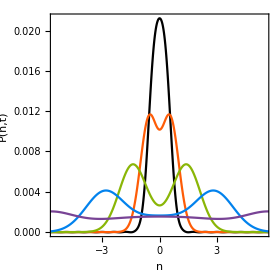

```mathematica
ts2 = {0.1,0.2,0.5,1.0,2.0};
Row@{ListLinePlot[Evaluate@Table[p[t,0.2],{t,ts2}],PlotRange->{{-5.5,5.5},All},Joined->True,
PlotStyle->COLORLIST,
PlotLegends->legend[NumberForm[#,{∞,1}]&/@ts2,{0.8,0.6}],
FrameLabel->{Style["n",Italic],Style["P(n,t)",Italic]},
AspectRatio->1,
BaseStyle->{FontFamily->"Times",20},
ImageSize->280
]," ",
ListLinePlot[Evaluate@Table[p[t,2.0],{t,ts2}],PlotRange->{{-5.5,5.5},All},Joined->True,
PlotStyle->COLORLIST,
FrameLabel->{Style["n",Italic],Style["P(n,t)",Italic]},
AspectRatio->1,
BaseStyle->{FontFamily->"Times",20},
ImageSize->280
]}
```

```mathematica
Clear[var];
Do[var[t,κ] = ((p[t,κ]⟦All,1⟧)^2 ).(p[t,κ]⟦All,2⟧),{κ,κs},{t,ts}];
```

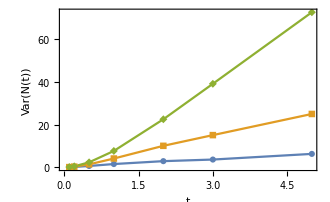

```mathematica
tmp=Table[{t,var[t,κ]},{κ,κs},{t,ts}];
ListLinePlot[tmp,PlotMarkers->Automatic,
FrameLabel->{"t","Var(N(t))"}]
```

### g^(1) functions: ⟨σ_z(t)σ_z(0)⟩

```mathematica
Clear[Δ,Ω,Γ];
Δ = 0;
H = Δ/2 σz + Ω σx;
c = √Γ σz;
ℒ = Liouvillian[H,{σz},{Γ}];
ρ = SteadyState[ℒ]//mf;
```

(1/2 | 0
0 | 1/2)

```mathematica
g1=FCSCorr[t,ρ,ℒ,σ0,σz,σz]//cf
```

ⅇ^(-t Γ) (Cosh[t √(Γ^2-4 Ω^2)]+(Γ Sinh[t √(Γ^2-4 Ω^2)])/(√(Γ^2-4 Ω^2)))

## Example D

### Stochastic trajectories when U = 0 (G ≠ 0)

{0,0,0.0692308}

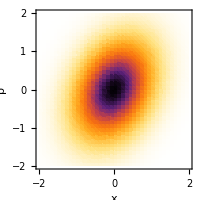

```mathematica
LoadBosonicOperators[nmax = 20];
Δ = 0.7;
G = -0.3;
κ = 1.0;
dt = 0.005;
tf = 3000.0;

H = Δ a†.a + (ⅈ G)/2(a†.a†-a.a);
c = √κ a;

ℒ = Liouvillian[H,{c}];
ρ = SteadyState[ℒ];
ψ0 = Basis[nmax,1];
W = WignerFunction[ρ,2,0.1];
Chop@{Tr[𝕏.ρ],Tr[ℙ.ρ],Tr[a†.a.ρ]}
ListDensityPlot[W,PlotRange->All,ImageSize->200,ColorFunction->(ColorData["SunsetColors",(1-#)]&),AspectRatio->1,
FrameLabel->{"x","p"}]
```

```mathematica
S=QuantumDiffusion[ψ0,H,{c/(√2),(-ⅈ c)/(√2)},dt,tf,None,2,None,False];
```

0h : 1m : 22s

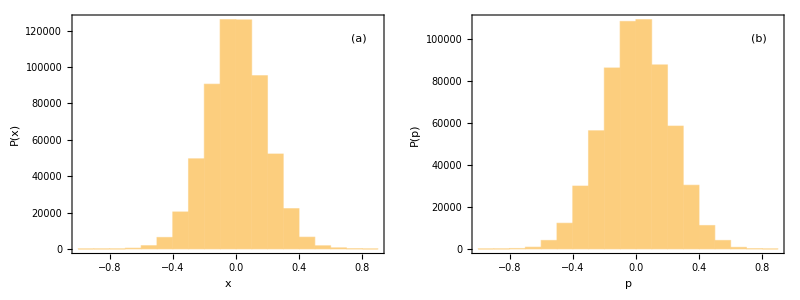

```mathematica
grid@{
Histogram[S["xave"][[All,1]],{0.1},Frame->True,FrameLabel->{"x","P(x)"}],
Histogram[S["xave"][[All,2]],{0.1},Frame->True,FrameLabel->{"p","P(p)"}]}
```

```mathematica
ListLinePlot[(1/(√2)S["xave"]),PlotStyle->Directive[Black,Thickness[0.0005]],AspectRatio->1,
Frame->True,FrameLabel->{"x","p"}]
```

-Graphics-

```mathematica
rasta@Show[
ListDensityPlot[W,PlotRange->All,ImageSize->400,ColorFunction->(ColorData["SunsetColors",(1-#)]&),AspectRatio->1],
ListLinePlot[(-1/(√2)S["xave"])[[1;;-1;;200]],PlotStyle->Directive[Red,Thickness[0.00005]]],
FrameLabel->{"x","p"}
]
```

-Graphics-

### Stochastic trajectories when U ≠ 0

```mathematica
LoadBosonicOperators[nmax = 20];
Δ = 0.;
G = 1.;
κ = 1.0;
dt = 0.002;
tf = 1000.0;
U = 1/3;

H = Δ a†.a + (ⅈ G)/2(a†.a†-a.a)+U/2 a†.a†.a.a;
c = √κ a;

ℒ = Liouvillian[H,{c}];
ρ = SteadyState[ℒ];
ψ0 = Basis[nmax,1];
W = WignerFunction[ρ,4,0.1];
Chop@{Tr[𝕏.ρ],Tr[ℙ.ρ],Tr[a†.a.ρ]}
```

{0,0,2.32429}

```mathematica
S=QuantumDiffusion[ψ0,H,c,dt,tf,None,2,expect[√2 ℙ,#]&];
```

0h : 1m : 17s

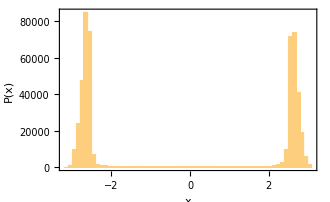

```mathematica
Histogram[S["xave"],{0.1},Frame->True,FrameLabel->{"x","P(x)"}]
```

```mathematica
rasta@Show[
ListDensityPlot[W,PlotRange->All,ImageSize->400,ColorFunction->(ColorData["SunsetColors",(1-#)]&),AspectRatio->1],
ListLinePlot[(1/(√2){S["xave"],S["f"]}ᵀ)[[1;;-1;;10]],PlotStyle->Directive[Black,Thickness[0.0005]]],
FrameLabel->{"x","p"}
]
```

-Graphics-

### Exact steady-state solution in the Gaussian case

H = Δ a†a + 1/2(G a† a† + G^* a a)

```mathematica
Clear[GaussianHamiltonian]
GaussianHamiltonian[AA_,BB_]:=Module[{A,B,ℍ,Ωℍ},
A = If[Length@Dimensions@AA==2,AA,{{AA}}];
B = If[Length@Dimensions@BB==2,BB,{{BB}}];
LoadPauliMatrices[];
ℍ = 1/2(σ0⊗(A+Aᵀ) + σz⊗(B+B*) + σy ⊗(Aᵀ-A) - ⅈ σx ⊗(B-B*));
Ωℍ = -ⅈ/2(σ0⊗(A-Aᵀ) - σy ⊗ (A+Aᵀ) -ⅈ σx ⊗(B+B*) +σz ⊗(B-B*));
{ℍ,Ωℍ}
]
```

```mathematica
GetCS[Θ_]:=Module[{ϕ = 1/(√2)({{1, 1}, {-ⅈ, ⅈ}}),𝒞,S,d = Length[Θ]/2},
𝒞 = PTr[Θ.(ϕ.σp.σm.ϕ† ⊗ Eye[d]),{1},{2,d}]- Eye[d]/2;
S = PTr[Θ.(ϕ.σm.ϕ†⊗Eye[d]),{1},{2,d}];
{𝒞,S}
]
```

```mathematica
Clear[Δ,G,κ]
{ℍ,Ωℍ}=GaussianHamiltonian[Δ,G]//Simplify;
Ωℍ//mf;

Γ = {{κ}};
𝒲 = -Ωℍ + 1/2 σ0⊗Γ//Simplify//mf;
Υ = 1/2 σ0 ⊗ Γ;
(*𝒲 = 𝒲/.Conjugate[G]->Gs//cf//mf;*)
```

(-1/2 ⅈ (G-Conjugate[G]) | -G/2+Δ-Conjugate[G]/2
1/2 (-G-2 Δ-Conjugate[G]) | 1/2 ⅈ (G-Conjugate[G]))

(1/2 (ⅈ G+κ-ⅈ Conjugate[G]) | 1/2 (G-2 Δ+Conjugate[G])
1/2 (G+2 Δ+Conjugate[G]) | 1/2 (-ⅈ G+κ+ⅈ Conjugate[G]))

```mathematica
Θ=LyapunovLinearSys[𝒲,Υ]//Simplify//mf;
```

((κ (-((2 G-2 Δ+ⅈ κ-2 Conjugate[Δ]+ⅈ Conjugate[κ]) (2 Δ+ⅈ κ+2 Conjugate[Δ]+ⅈ Conjugate[κ]))+Conjugate[G] (-4 Δ+2 ⅈ κ-4 Conjugate[Δ]+2 ⅈ Conjugate[κ])) (κ+Conjugate[κ]))/(16 Conjugate[Δ]^4-16 G Conjugate[G] (κ+Conjugate[κ])^2+8 Conjugate[Δ]^2 (-4 Δ^2+κ^2+2 κ Conjugate[κ]+Conjugate[κ]^2)+(4 Δ^2+κ^2+2 κ Conjugate[κ]+Conjugate[κ]^2)^2) | (-2 κ Conjugate[G] (κ+Conjugate[κ]) (2 ⅈ Δ+κ+2 ⅈ Conjugate[Δ]+Conjugate[κ])+2 ⅈ κ (2 Δ+ⅈ κ+2 Conjugate[Δ]+ⅈ Conjugate[κ]) (-2 ⅈ Δ^2+G κ-Δ κ+2 ⅈ Conjugate[Δ]^2+(G-Δ) Conjugate[κ]+Conjugate[Δ] (κ+Conjugate[κ])))/(16 Conjugate[Δ]^4-16 G Conjugate[G] (κ+Conjugate[κ])^2+8 Conjugate[Δ]^2 (-4 Δ^2+κ^2+2 κ Conjugate[κ]+Conjugate[κ]^2)+(4 Δ^2+κ^2+2 κ Conjugate[κ]+Conjugate[κ]^2)^2)
-(2 κ (Conjugate[G] (κ+Conjugate[κ]) (2 ⅈ Δ+κ+2 ⅈ Conjugate[Δ]+Conjugate[κ])-ⅈ (2 Δ+ⅈ κ+2 Conjugate[Δ]+ⅈ Conjugate[κ]) (2 ⅈ Δ^2+G κ+Δ κ-2 ⅈ Conjugate[Δ]^2+(G+Δ) Conjugate[κ]-Conjugate[Δ] (κ+Conjugate[κ]))))/(16 Conjugate[Δ]^4-16 G Conjugate[G] (κ+Conjugate[κ])^2+8 Conjugate[Δ]^2 (-4 Δ^2+κ^2+2 κ Conjugate[κ]+Conjugate[κ]^2)+(4 Δ^2+κ^2+2 κ Conjugate[κ]+Conjugate[κ]^2)^2) | (κ ((2 G+2 Δ-ⅈ κ+2 Conjugate[Δ]-ⅈ Conjugate[κ]) (2 Δ+ⅈ κ+2 Conjugate[Δ]+ⅈ Conjugate[κ])+Conjugate[G] (4 Δ-2 ⅈ κ+4 Conjugate[Δ]-2 ⅈ Conjugate[κ])) (κ+Conjugate[κ]))/(16 Conjugate[Δ]^4-16 G Conjugate[G] (κ+Conjugate[κ])^2+8 Conjugate[Δ]^2 (-4 Δ^2+κ^2+2 κ Conjugate[κ]+Conjugate[κ]^2)+(4 Δ^2+κ^2+2 κ Conjugate[κ]+Conjugate[κ]^2)^2))

```mathematica
{𝒞,S}=FullSimplify[GetCS[Θ]/.Gs->Conjugate[G],{Δ>0,κ>0}];
𝒞//mf;
S//mf;
```

((2 G Conjugate[G])/(4 Δ^2+κ^2-4 G Conjugate[G]))

(-(G (2 Δ+ⅈ κ))/(4 Δ^2+κ^2-4 G Conjugate[G]))

#### Checking with numerical simulations

```mathematica
LoadBosonicOperators[nmax=50];
Δ = 0.8;
κ = 1.88;
G = 0.1 -0.19 ⅈ;
H = Δ a†.a + 1/2(G a†.a† + G* a.a);
ℒ = Liouvillian[H,{a},{κ}];
ρ = SteadyState[ℒ];

{ℍ,Ωℍ}=GaussianHamiltonian[Δ,G];
Γ = {{κ}};
𝒲 = -Ωℍ + 1/2 σ0⊗Γ;
Υ = 1/2 σ0 ⊗ Γ;
Θ=LyapunovLinearSys[𝒲,Υ]//Simplify;
{𝒞,S}=FullSimplify[GetCS[Θ]/.Gs->Conjugate[G],{Δ>0,κ>0}];

{Tr[ρ.a†.a]-𝒞[[1,1]]}//Chop
{Tr[ρ.a.a]-S[[1,1]]}//Chop

RB= {𝕏,ℙ};
ΘB = 1/2 Table[Tr[ℂ[RB[[i]],RB[[j]],-1].ρ],{i,2},{j,2}];
ΘB-Θ//mf;
```

{-7.26343×10^-10}

{0.-2.30134×10^-10 ⅈ}

(-6.89378×10^-10 | -2.30134×10^-10
-2.30134×10^-10 | -8.42843×10^-10)

### F, S and D in the Gaussian case (G ≠ 0 and ϵ = 0)

#### Comparison with full numerics

```mathematica
LoadBosonicOperators[nmax=50];
Clear[Δ,G,κ,ω];
Δ = 0.;
κ = 1.43;
𝒢 = 0.2;
G = ⅈ 𝒢;
ϕ = π/2;
c = √κ a  ⅇ^(-ⅈ ϕ);
H = Δ a†.a + 1/2(G a†.a† + G* a.a);
ℒ = Liouvillian[H,{c}];
ρ = SteadyState[ℒ];
ω=0.02;

𝕃=BDFCSload[{{Δ}},{{κ},{0}},{{1},{0}},ϵ=0,"boson",{{ G}},{{ϕ},{0}}];

S1=FCSPowerSpectrum[{ω},ρ,ℒ,{c},1]
S2 = BDFCSPowerSpectrum[ω,𝕃]

S1=FCSPowerSpectrum[{ω},ρ,ℒ,{c},1,"diffusion"]
S2 = BDFCSPowerSpectrum[ω,𝕃,"diffusion"]
```

0.148865

0.148865

0.317117

0.317117

#### Loading up analytical formulas

```mathematica
Clear[Δ,G,κ,ω,ϕ,𝒢];
Δ=0;
𝕃=BDFCSload[{{Δ}},{{κ},{0}},{{1},{0}},ϵ=0,"boson",{{ⅈ 𝒢}},{{ϕ},{0}}];
𝕃=cf/@𝕃
```

<|size→2,s→1,statistic→boson,Ω→{{0,1},{-1,0}},𝕀→{{1,0},{0,1}},γp→{{0}},γm→{{κ}},νp→{{0}},νm→{{1}},Γ→{{κ}},𝒲→{{1/2 (-2 𝒢+κ),0},{0,𝒢+κ/2}},Υ→{{κ/2,0},{0,κ/2}},Vj→{{κ/2,(ⅈ κ)/2},{-(ⅈ κ)/2,κ/2}},Vd→{{(ⅇ^(-ⅈ ϕ) √κ)/(√2),0},{0,(√κ (ⅈ Cos[ϕ]+Sin[ϕ]))/(√2)}},Θ→{{-κ/(4 𝒢-2 κ),0},{0,κ/(4 𝒢+2 κ)}},r→{0,0},o→{1,1},Jj→(2 𝒢^2 κ)/(-4 𝒢^2+κ^2),Jd→0,Kj→(2 𝒢^2 κ)/(-4 𝒢^2+κ^2),Kd→1|>

#### Lyapunov stuff and V matrices

```mathematica
𝕃["𝒲"]//Expand//mf;
```

(-𝒢+κ/2 | 0
0 | 𝒢+κ/2)

```mathematica
𝕃["Υ"]//mf;
```

(κ/2 | 0
0 | κ/2)

```mathematica
𝕃["Θ"]//cf//mf;
```

(-κ/(4 𝒢-2 κ) | 0
0 | κ/(4 𝒢+2 κ))

```mathematica
GetCS[𝕃["Θ"]]//First//cf
```

{{-(2 𝒢^2)/(4 𝒢^2-κ^2)}}

```mathematica
𝕃["Vd"]//mf;
```

((ⅇ^(-ⅈ ϕ) √κ)/(√2) | 0
0 | (√κ (ⅈ Cos[ϕ]+Sin[ϕ]))/(√2))

```mathematica
𝕃["Jj"]//cf
𝕃["Jd"]//cf
```

(2 𝒢^2 κ)/(-4 𝒢^2+κ^2)

0

#### Quantum diffusion

```mathematica
BDFCSPowerSpectrum[ω,𝕃,"diffusion"]-1/.𝒢->G//cf
```

(8 G κ (4 G κ+(4 G^2+κ^2+4 ω^2) Cos[2 ϕ]))/(((-2 G+κ)^2+4 ω^2) ((2 G+κ)^2+4 ω^2))

```mathematica
ⅇ^(-2 ⅈ ϕ) (4 𝒢^2+4 ⅇ^(2 ⅈ ϕ) 𝒢 κ+κ^2+4 ω^2)//Expand//cf
```

4 𝒢 κ+ⅇ^(-2 ⅈ ϕ) (4 𝒢^2+κ^2+4 ω^2)

```mathematica
Sx=BDFCSPowerSpectrum[ω,𝕃,"diffusion"]/.ϕ->0//cf
Sp=BDFCSPowerSpectrum[ω,𝕃,"diffusion"]/.ϕ->π/2//cf
```

1+(8 𝒢 κ)/((-2 𝒢+κ)^2+4 ω^2)

1-(8 𝒢 κ)/((2 𝒢+κ)^2+4 ω^2)

```mathematica
((2 𝒢+κ)^2+4 ω^2)/4//cf
```

1/4 (2 𝒢+κ)^2+ω^2

```mathematica
Manipulate[Plot[Evaluate[{Sx,Sp}/.κ->1/.𝒢->G],{ω,-3,3}],{{G,0.1},0,1/2}]
```

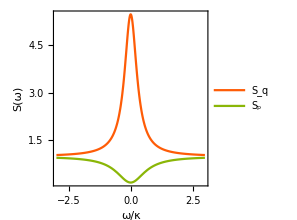

```mathematica
plt1=Plot[Evaluate[{Sx,Sp}/.κ->1/.𝒢->0.2],{ω,-3,3},
PlotStyle->Rest@COLORLIST,
PlotLegends->legend[{"S_q","S_p"},{0.8,0.7}],
FrameLabel->{"ω/κ","S(ω)"},
AspectRatio->1,
ImageSize->220
]
```

```mathematica
Dgen=BDFCSNoise[𝕃,"diffusion"]//cf
Dx=BDFCSNoise[𝕃,"diffusion"]/.ϕ->0//cf
Dp=BDFCSNoise[𝕃,"diffusion"]/.ϕ->π/2//cf
```

(ⅇ^(-2 ⅈ ϕ) (4 𝒢^2+4 ⅇ^(2 ⅈ ϕ) 𝒢 κ+κ^2) (4 𝒢 κ+ⅇ^(2 ⅈ ϕ) (4 𝒢^2+κ^2)))/((-4 𝒢^2+κ^2)^2)

(2 𝒢+κ)^2/(-2 𝒢+κ)^2

(-2 𝒢+κ)^2/(2 𝒢+κ)^2

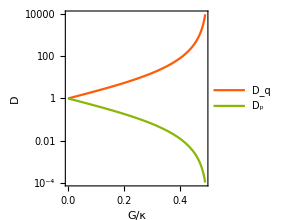

```mathematica
yticks = logticks[-4,4,2,2.2];
plt2=LogPlot[Evaluate[{Dx,Dp}/.κ->1],{𝒢,0,0.49},
PlotStyle->Rest@COLORLIST,
FrameLabel->{"G/κ",Style["D",Italic]},
PlotLegends->legend[{"D_q","D_p"},{0.57,0.85},LegendLayout->"Row"],
FrameTicks->{{yticks,None},{Automatic,Automatic}},
AspectRatio->1,
ImageSize->220
]
```

```mathematica
Fq=BDFCSTwoPointFunction[τ,𝕃,"diffusion"]/.ϕ->0//cf
Fp=BDFCSTwoPointFunction[τ,𝕃,"diffusion"]/.ϕ->π/2//cf
```

-(2 ⅇ^(𝒢 τ-(κ τ)/2) 𝒢 κ)/(2 𝒢-κ)

-(2 ⅇ^(-1/2 (2 𝒢+κ) τ) 𝒢 κ)/(2 𝒢+κ)

```mathematica
Manipulate[Plot[Evaluate[{Fq,Fp}/.κ->1/.𝒢->G],{τ,0,10}],{{G,0.1},0,1/2}]
```

```mathematica
Fq+Fp//cf
```

(4 ⅇ^(-(κ τ)/2) 𝒢 κ (2 𝒢 Cosh[𝒢 τ]+κ Sinh[𝒢 τ]))/(-4 𝒢^2+κ^2)

```mathematica
Fq-Fp//cf
```

(4 ⅇ^(-(κ τ)/2) 𝒢 κ (κ Cosh[𝒢 τ]+2 𝒢 Sinh[𝒢 τ]))/(-4 𝒢^2+κ^2)

#### Quantum jumps

```mathematica
𝕃["Vj"]//mf;
```

(κ/2 | (ⅈ κ)/2
-(ⅈ κ)/2 | κ/2)

```mathematica
σy//mf;
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
J=𝕃["Jj"]
```

(2 𝒢^2 κ)/(-4 𝒢^2+κ^2)

```mathematica
F=cf@BDFCSTwoPointFunction[t,𝕃]
```

(ⅇ^(-t (2 𝒢+κ)) 𝒢^2 κ^2 ((-2 𝒢+κ)^2+ⅇ^(4 t 𝒢) (2 𝒢+κ)^2))/(2 (-4 𝒢^2+κ^2)^2)

```mathematica
g2 = F/J^2+1//cf
```

1+(ⅇ^(-t (2 𝒢+κ)) ((-2 𝒢+κ)^2+ⅇ^(4 t 𝒢) (2 𝒢+κ)^2))/(8 𝒢^2)

```mathematica
ⅇ^(-t (2 𝒢+κ))ⅇ^(4 t 𝒢)//cf
```

ⅇ^(2 t 𝒢-t κ)

```mathematica
g2/.t->0//cf
```

2+κ^2/(4 𝒢^2)

```mathematica
Manipulate[Plot[g2/.κ->1/.𝒢->G,{t,0,10}],{{G,0.25},0,0.6}]
```

```mathematica
Sj=BDFCSPowerSpectrum[ω,𝕃]
```

(2 𝒢^2 κ)/(-4 𝒢^2+κ^2)+κ (-(𝒢^2 κ)/((2 𝒢-κ)^2 (2 𝒢-κ-2 ⅈ ω+2 Conjugate[𝒢]-Conjugate[κ]))-(𝒢^2 κ)/((2 𝒢-κ)^2 (2 𝒢-κ+2 ⅈ ω+2 Conjugate[𝒢]-Conjugate[κ])))+κ ((𝒢^2 κ)/((2 𝒢+κ)^2 (2 𝒢+κ-2 ⅈ ω+2 Conjugate[𝒢]+Conjugate[κ]))+(𝒢^2 κ)/((2 𝒢+κ)^2 (2 𝒢+κ+2 ⅈ ω+2 Conjugate[𝒢]+Conjugate[κ])))

```mathematica
Sj-(2 𝒢^2 κ)/(-4 𝒢^2+κ^2)//ComplexExpand
```

-(8 𝒢^3 κ^2)/((2 𝒢-κ)^2 ((4 𝒢-2 κ)^2+4 ω^2))+(4 𝒢^2 κ^3)/((2 𝒢-κ)^2 ((4 𝒢-2 κ)^2+4 ω^2))+(8 𝒢^3 κ^2)/((2 𝒢+κ)^2 ((4 𝒢+2 κ)^2+4 ω^2))+(4 𝒢^2 κ^3)/((2 𝒢+κ)^2 ((4 𝒢+2 κ)^2+4 ω^2))

```mathematica
(2 𝒢-κ) (2 𝒢+κ)//cf
```

4 𝒢^2-κ^2

```mathematica
-(8 𝒢^3 κ^2)/((2 𝒢-κ)^2 ((4 𝒢-2 κ)^2+4 ω^2))+(4 𝒢^2 κ^3)/((2 𝒢-κ)^2 ((4 𝒢-2 κ)^2+4 ω^2))//cf
```

-(𝒢^2 κ^2)/((2 𝒢-κ)^3+(2 𝒢-κ) ω^2)

```mathematica
(8 𝒢^3 κ^2)/((2 𝒢+κ)^2 ((4 𝒢+2 κ)^2+4 ω^2))+(4 𝒢^2 κ^3)/((2 𝒢+κ)^2 ((4 𝒢+2 κ)^2+4 ω^2))//cf
```

(𝒢^2 κ^2)/((2 𝒢+κ)^3+(2 𝒢+κ) ω^2)

```mathematica
Sj2 = (2 𝒢^2 κ)/(-4 𝒢^2+κ^2) + (𝒢^2 κ^2)/((2 𝒢+κ)^3+(2 𝒢+κ) ω^2) -(𝒢^2 κ^2)/((2 𝒢-κ)^3+(2 𝒢-κ) ω^2);
Sj-Sj2//cf
```

0

```mathematica
COLORLIST
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]}

```mathematica
Manipulate[Plot[Evaluate[{Sj}/.κ->1/.𝒢->G],{ω,-3,3}],{{G,0.1},0,1/2}]
```

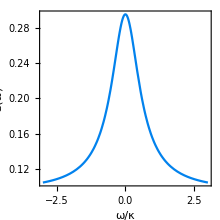

```mathematica
plt3=Plot[Evaluate[{Sj}/.κ->1/.𝒢->0.2],{ω,-3,3},
PlotStyle->COLORLIST[[4]],
PlotLegends->legend[{"S_q","S_p"},{0.8,0.7}],
FrameLabel->{"ω/κ","S(ω)"},
AspectRatio->1,
ImageSize->220
]
```

```mathematica
𝒟=Sj/.ω->0//cf
```

-(4 𝒢^2 κ (8 𝒢^4+2 𝒢^2 κ^2+κ^4))/((4 𝒢^2-κ^2)^3)

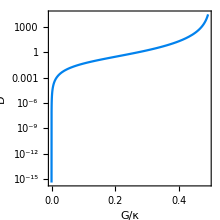

```mathematica
yticks = logticks[-14,4,4,2.2];
plt4=LogPlot[Evaluate[𝒟/.κ->1],{𝒢,0,0.49},
PlotStyle->COLORLIST[[4]],
FrameTicks->{{yticks,None},{Automatic,Automatic}},
FrameLabel->{"G/κ",Style["D",Italic]},
AspectRatio->1,
ImageSize->220
]
```

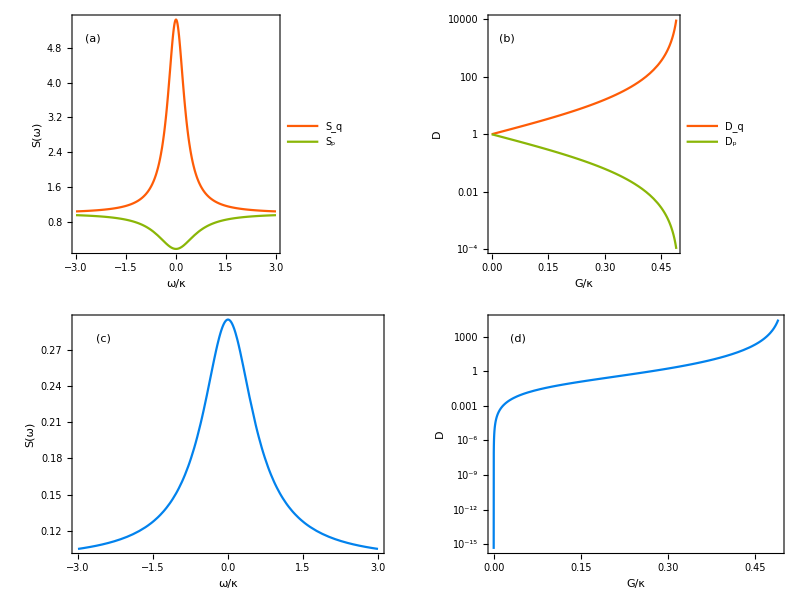

```mathematica
grid[{plt1,plt2,plt3,plt4},2,{0.1,0.9}]
Export[dirG<>"ExampleD_parametric_oscillator_Gaussian.pdf",%];
```

#### g2 function for thermal light

```mathematica
Clear[Δ,G,κ,ω,ϕ,𝒢];
Δ=0;
𝕃=BDFCSload[{{Δ}},{{κ (nb+1)},{κ nb}},{{1},{0}},ϵ=0,"boson",{{ⅈ 𝒢}},{{ϕ},{0}}];
𝕃=cf/@𝕃
```

<|size→2,s→1,statistic→boson,Ω→{{0,1},{-1,0}},𝕀→{{1,0},{0,1}},γp→{{nb κ}},γm→{{(1+nb) κ}},νp→{{0}},νm→{{1}},Γ→{{κ}},𝒲→{{1/2 (-2 𝒢+κ),0},{0,𝒢+κ/2}},Υ→{{(1/2+nb) κ,0},{0,(1/2+nb) κ}},Vj→{{1/2 (1+nb) κ,1/2 ⅈ (1+nb) κ},{-1/2 ⅈ (1+nb) κ,1/2 (1+nb) κ}},Vd→{{(ⅇ^(-ⅈ ϕ) √((1+nb) κ))/(√2),0},{0,(√((1+nb) κ) (ⅈ Cos[ϕ]+Sin[ϕ]))/(√2)}},Θ→{{-(κ+2 nb κ)/(4 𝒢-2 κ),0},{0,(κ+2 nb κ)/(4 𝒢+2 κ)}},r→{0,0},o→{1,1},Jj→((1+nb) κ (2 𝒢^2+nb κ^2))/(-4 𝒢^2+κ^2),Jd→0,Kj→((1+nb) κ (2 𝒢^2+nb κ^2))/(-4 𝒢^2+κ^2),Kd→1|>

```mathematica
J=𝕃["Jj"]
```

((1+nb) κ (2 𝒢^2+nb κ^2))/(-4 𝒢^2+κ^2)

```mathematica
F=cf@BDFCSTwoPointFunction[t,𝕃]
```

1/2 (1+nb)^2 κ^2 ((ⅇ^(-t (2 𝒢+κ)) (𝒢-nb κ)^2)/(2 𝒢+κ)^2+(ⅇ^(2 t 𝒢-t κ) (𝒢+nb κ)^2)/(-2 𝒢+κ)^2)

```mathematica
g2 = F/J^2+1//cf
```

1+(ⅇ^(-2 t (𝒢+κ)) (ⅇ^(t κ) (-2 𝒢+κ)^2 (𝒢-nb κ)^2+ⅇ^(t (4 𝒢+κ)) (2 𝒢+κ)^2 (𝒢+nb κ)^2))/(2 (2 𝒢^2+nb κ^2)^2)

```mathematica
g20=g2/.t->0//cf
```

(8 𝒢^4+(1+4 nb (3+nb)) 𝒢^2 κ^2+2 nb^2 κ^4)/((2 𝒢^2+nb κ^2)^2)

```mathematica
Limit[g20,𝒢->0]
```

2

```mathematica
Limit[g20,nb->0]//cf
```

2+κ^2/(4 𝒢^2)

```mathematica
g20-2//cf
```

((1+2 nb)^2 𝒢^2 κ^2)/((2 𝒢^2+nb κ^2)^2)

```mathematica
Limit[Limit[g20,nb->0],𝒢->0]
```

∞ Sign[κ]^2

```mathematica
Collect[(1+4 nb (3+nb)) 𝒢^2 κ^2+2 nb^2 κ^4,𝒢]
```

(1+4 nb (3+nb)) 𝒢^2 κ^2+2 nb^2 κ^4

## Hasegawa’s bound

### Example A

```mathematica
Clear[γ];
H = (0 Δ)/2 σz+Ω σx;
ℒ = Liouvillian[H,{σm},{γ}];
c = √γ σm;
ρ = SteadyState[ℒ]//cf//mf;
```

((4 Ω^2)/(γ^2+8 Ω^2) | -(2 ⅈ γ Ω)/(γ^2+8 Ω^2)
(2 ⅈ γ Ω)/(γ^2+8 Ω^2) | (γ^2+4 Ω^2)/(γ^2+8 Ω^2))

```mathematica
f=GammelmarkMolmerMFisher[ρ,ℒ,H,H,{c},{c/2}]//cf
```

(4 Ω^2 (γ^2+32 Ω^2))/(γ^3+8 γ Ω^2)

```mathematica
J = FCSAverage[ρ,ℒ,{c},{1}]//cf
𝒟 = FCSNoise[ρ,ℒ,{c},{1}]//cf
```

(4 γ Ω^2)/(γ^2+8 Ω^2)

(4 γ Ω^2 (γ^4-8 γ^2 Ω^2+64 Ω^4))/((γ^2+8 Ω^2)^3)

```mathematica
(*Plot[Evaluate[{𝒟/J^2,1/f}/.γ->1/2/.Ω->1],{Δ,0.,5.}]*)
```

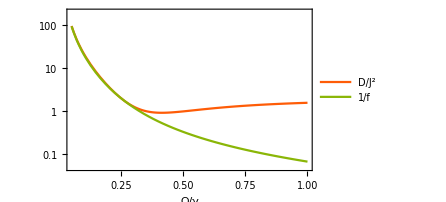

```mathematica
yticks=logticks[-1,2,1];
LogPlot[Evaluate[{𝒟/J^2,1/f}/.γ->1],{Ω,0.05,1},
PlotStyle->Rest@COLORLIST,
PlotLegends->legend[{"D/J^2","1/f"},{0.7,0.7}],
FrameTicks->{{yticks,None},{Automatic,Automatic}},
PlotRange->{0.05,200},
FrameLabel->{"Ω/γ",None}
]
(*Export[dirG<>"hasegawa.pdf",%];*)
```

### Example B

```mathematica
Clear[γ];
simp = {γ1>0, γ2>0, 0<f1<1,0<f2<1};
H = ω σp.σm;
cops = {σm,σp,σm,σp};
rates = {γ1(1-f1),γ1 f1,γ2(1-f2),γ2 f2};
ℒ = Liouvillian[0 σz,cops,rates];
ccops = √rates cops;
ρ = SteadyState[ℒ]//cf//mf;
```

((f1 γ1+f2 γ2)/(γ1+γ2) | 0
0 | (γ1-f1 γ1+γ2-f2 γ2)/(γ1+γ2))

```mathematica
J = FullSimplify[FCSAverage[ρ,ℒ,ccops{-1,1,0,0}],simp]
𝒟 = FullSimplify[FCSNoise[ρ,ℒ,ccops{-1,1,0,0}],simp]
```

(γ1 (-2 f1^2 γ1+f2 γ2+f1 (2 γ1+γ2-2 f2 γ2)))/(γ1+γ2)

1/(γ1+γ2)^3 γ1 (-4 (-1+f1) f1 (1+2 (-1+f1) f1) γ1^3+(f2+f1 (9-10 f2+8 f1 (-2+f1+3 f2-2 f1 f2))) γ1^2 γ2+2 (-3 (-1+f1) f1+f2+4 (-1+f1) f1 f2-(1-2 f1)^2 f2^2) γ1 γ2^2+(f1+f2-2 f1 f2) γ2^3)

```mathematica
f=FullSimplify[GammelmarkMolmerMFisher[ρ,ℒ,H,H,ccops,ccops/2],simp]
```

-(2 ((-1+f1) γ1+(-1+f2) γ2) (f1 γ1+f2 γ2) (1764+(γ1+γ2)^2))/(γ1+γ2)^3

```mathematica
𝒟/J^2 f//cf
```

-((2 ((-1+f1) γ1+(-1+f2) γ2) (f1 γ1+f2 γ2) (-4 (-1+f1) f1 (1+2 (-1+f1) f1) γ1^3+(f2+f1 (9-10 f2+8 f1 (-2+f1+3 f2-2 f1 f2))) γ1^2 γ2+2 (-3 (-1+f1) f1+f2+4 (-1+f1) f1 f2-(1-2 f1)^2 f2^2) γ1 γ2^2+(f1+f2-2 f1 f2) γ2^3) (1764+(γ1+γ2)^2))/(γ1 (γ1+γ2)^4 (-2 f1^2 γ1+f2 γ2+f1 (2 γ1+γ2-2 f2 γ2))^2))

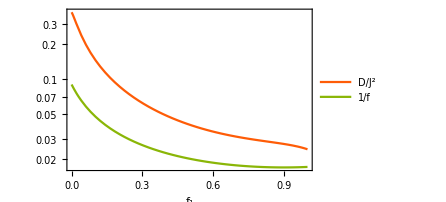

```mathematica
LogPlot[Evaluate[{𝒟/J^2,1/f}/.{γ1->50,γ2->50,f2->0.1}],{f1,0,1},
PlotStyle->Rest@COLORLIST,
PlotLegends->legend[{"D/J^2","1/f"},{0.7,0.7}],
FrameLabel->{"f_1",None}
]
```

### Example C

```mathematica
Clear[Δ];
Δ = 0;
H = Δ/2 σz + Ω σx;
c = √Γ σz;
ℒ = Liouvillian[H,{σz},{Γ}];
ρ = SteadyState[ℒ]//mf;
```

(1/2 | 0
0 | 1/2)

```mathematica
f=FullSimplify[GammelmarkMolmerMFisher[ρ,ℒ,H,H,{c},{c}/2]//cf]
```

Γ+(4 Ω^2)/Γ

```mathematica
J = FullSimplify[FCSAverage[ρ,ℒ,{c},{1}]//cf]
𝒟 = FullSimplify[FCSNoise[ρ,ℒ,{c},{1}]//cf]
```

Γ

Γ

```mathematica
𝒟/J^2 f//cf
```

1+(4 Ω^2)/Γ^2

```mathematica
J = FullSimplify[FCSAverage[ρ,ℒ,{c},{1},"homodyne"]//cf]
𝒟 = FullSimplify[FCSNoise[ρ,ℒ,{c},{1},"homodyne"]//cf]
```

0

1+(4 Γ^2)/Ω^2

## Filters

```mathematica
ap = 1.3;
plt1=BodePlot[Evaluate@Table[ButterworthFilterModel[{"Lowpass",n,1.}],{n,1,4}],{0.05,50},GridLines->Automatic,
PlotLayout->"Magnitude",
PlotStyle->COLORLIST,
PlotLegends->legend[{1,2,3,4},{0.25,0.42}],
FrameLabel->{"ω/γ","20 log_10G(ω)"},
BaseStyle->{FontFamily->"Times",16,Black},
FrameStyle->Black,
AspectRatio->1/ap
];

plt2=BodePlot[Evaluate@Table[ButterworthFilterModel[{"Highpass",n,1.}],{n,1,4}],{0.05,50},GridLines->Automatic,
PlotLayout->"Magnitude",
PlotStyle->COLORLIST,
PlotLegends->legend[{1,2,3,4},{0.75,0.42}],
FrameLabel->{"ω/γ","20 log_10G(ω)"},
BaseStyle->{FontFamily->"Times",16,Black},
FrameStyle->Black,
AspectRatio->1/ap
];

plt3=BodePlot[Evaluate@Table[ButterworthFilterModel[{"Bandpass",n,{1,10}}],{n,1,4}],{0.05,100},GridLines->Automatic,
PlotLayout->"Magnitude",
PlotStyle->COLORLIST,
PlotLegends->legend[{1,2,3,4},{0.55,0.42}],
FrameLabel->{"ω/ω_l","20 log_10G(ω)"},
BaseStyle->{FontFamily->"Times",16,Black},
FrameStyle->Black,
AspectRatio->1/ap
];
```

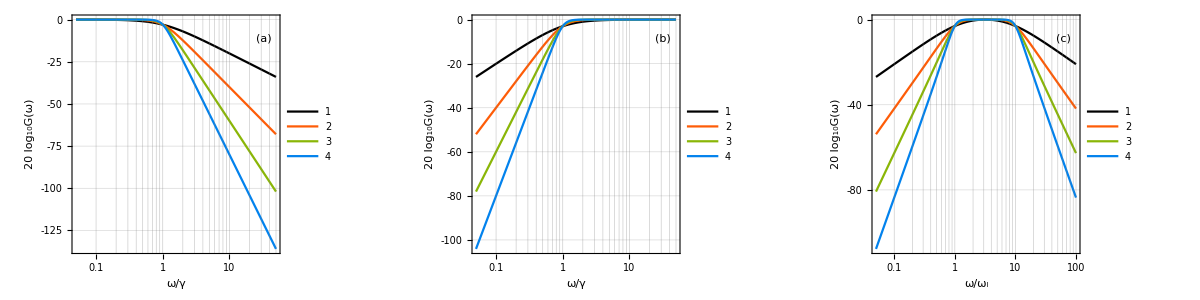

```mathematica
grid[{plt1,plt2,plt3}]
```

```mathematica
(*Export[dirG<>"gain.pdf",%];*)
```

## Other

### Simulating the power spectrum

```mathematica
H= σx + σz/2;
γ = 0.5;
cops =√γ{σm, σp};
ψ0 = {1,1}/√2;
ℒ = Liouvillian[H,cops];
ρ = SteadyState[ℒ];
ts = Range[0,14.0,0.001];
ts2 = Range[0,5000.0,0.001];
{ψ2,jumpList2}=QuantumJumpUnravelling[H,cops,ψ0,ts2,2];
```

```mathematica
curr=jumpList2⟦All,2⟧/.{1->-1,2->1};
current =ReplacePart[ConstantArray[0,Length@ts2],Thread[jumpList2⟦All,1⟧->curr]];
```

```mathematica
ωs = range[-10,10,0.1];
𝒮 = FCSPowerSpectrum[ωs,ρ,ℒ,cops,{-1,1}];
```

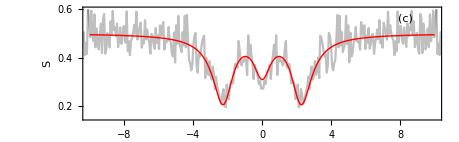

```mathematica
Δt = First@Differences@ts2;
nave = 200;
current2 = Total/@Partition[current,nave];
plot3c=Show[
ListLinePlot[{#⟦1⟧,#⟦2⟧/(nave^2 Δt^2)}&/@PowerSpectrum[current2,nave Δt,50],
PlotRange->{{-10,10},{0.15,0.6}},
PlotStyle->Directive[Black,Opacity[0.25]]
],
ListLinePlot[Re@𝒮,PlotStyle->{Red,Thick}],
AspectRatio->1/(2GoldenRatio),
FrameLabel->{"ω",Style["S",Italic]},
Epilog->Text["(c)",Scaled[{0.9,0.9}]],
ImageSize->460
]
```

```mathematica
nave = 15;
current2 = Total/@Partition[current,nave];
nave3 = 32;
current3 = Total/@Partition[current,nave3];
rasta@ListLinePlot[{
{#⟦1⟧,#⟦2⟧/(nave^2 Δt^2)}&/@PowerSpectrum[current2,nave Δt,20],
{#⟦1⟧,#⟦2⟧/(nave3^2 Δt^2)}&/@PowerSpectrum[current3,nave3 Δt,20]
},

PlotRange->{{-10,10},All},
FrameLabel->{"ω","S"}
]
```

-Graphics-

### Power spectrum correlations for example A

```mathematica
γ = 1;
Δ = 0;
Ω = 1;
Nb = 0.2;
H= Ω σx + Δ σz/2;
γm = γ (Nb+1);
γp = γ Nb;
cops ={√γm σm, √γp σp};
ψ0 = {1,1}/√2;
ℒ = Liouvillian[H,cops];
ρ = SteadyState[ℒ];
```

```mathematica
S=FCSEigenPowerSpectrum[ρ,ℒ,cops,{{1,0},{0,1}}]
```

K$51838-Table[Chop[Total[Table[Υ$51838⟦β,α,j⟧/(λ$51838⟦j⟧-ⅈ #1)+Υ$51838⟦α,β,j⟧/(λ$51838⟦j⟧+ⅈ #1),{j,Length[λ$51838]}]]],{α,R$51838},{β,R$51838}]&

```mathematica
F = FCSEigenTwoPointFunction[ρ,ℒ,cops,{{1,0},{0,1}}]
```

Table[Chop[Total[Table[Exp[λ$51846⟦j⟧ #1] Υ$51846⟦β,α,j⟧,{j,Length[λ$51846]}]]],{α,R$51846},{β,R$51846}]&

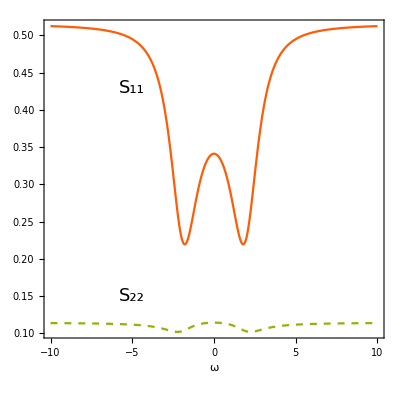
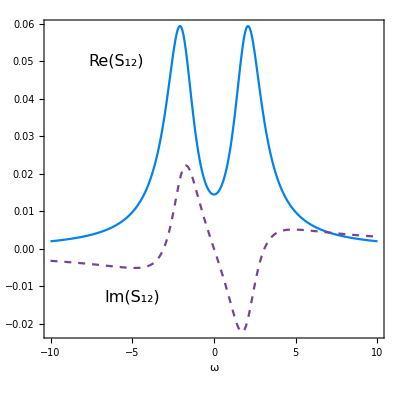
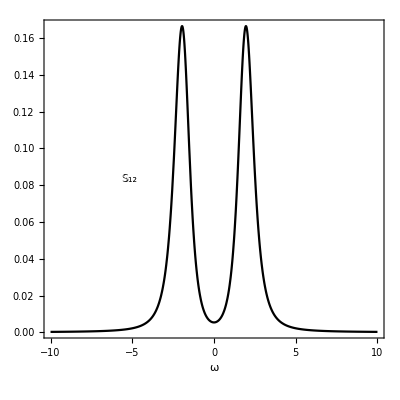

```mathematica
Row@{Plot[{S[ω][[1,1]],S[ω][[2,2]]},{ω,-10,10},
ImageSize->{Automatic,200},
PlotStyle->{COLORLIST[[2]],Directive[COLORLIST[[3]],Dashed]},
AspectRatio->1,
FrameLabel->{"ω",None},
(*PlotLegends->legend[{"S_11","S_22"},{0.2,0.5},framed->False],*)
Epilog->{
Text[Style["S_11",Italic,18],{-5,0.43}],
Text[Style["S_22",Italic,18],{-5,0.15}]
}
],
Plot[{Re@S[ω][[1,2]],Im@S[ω][[1,2]]},{ω,-10,10},
ImageSize->{Automatic,200},
PlotStyle->{COLORLIST[[4]],Directive[COLORLIST[[5]],Dashed]},
AspectRatio->1,
FrameLabel->{"ω",None},
Epilog->{
Text[Style["Re(S_12)",16],{-6,0.05}],
Text[Style["Im(S_12)",16],{-5,-0.013}]
}

],
Plot[{Abs[S[ω][[1,2]]]^2/(S[ω][[1,1]] S[ω][[2,2]])},{ω,-10,10},
ImageSize->{Automatic,200},
PlotStyle->Black,
AspectRatio->1,
FrameLabel->{"ω",None},
PlotLegends->Placed["𝕊_12",Scaled[{0.25,0.5}]]
]
}
```

### Power spectrum correlations for example B

```mathematica
Clear[γ,fL,fR,f,ω];
H = σz;
cops = {√(γ(1-fL))σm,√(γ fL)σp,√(γ(1-fR))σm,√(γ fR)σp};
(*cops = {√(γ gL)σm,√(γ fL)σp,√(γ gR)σm,√(γ fR)σp};*)
simp = {γ>0,0<fL<1,0<fR<1,0<gL<1,0<gR<1};
ℒ = FullSimplify[Liouvillian[H,cops],simp]//cf//mf;
ρ = AnalyticalSteadyState[ℒ]//cf//mf;
```

((-2+fL+fR) γ | 0 | 0 | (fL+fR) γ
0 | 2 ⅈ-γ | 0 | 0
0 | 0 | -2 ⅈ-γ | 0
-((-2+fL+fR) γ) | 0 | 0 | -((fL+fR) γ))

((fL+fR)/2 | 0
0 | 1/2 (2-fL-fR))

```mathematica
S=FullSimplify[FCSPowerSpectrum[ω,ρ,ℒ,cops,{{1,-1,0,0},{0,0,1,-1}}],{γ>0,0<fL<1,0<fR<1}]//mf;
```

((-2 (-2+fL+fR) (fL+fR) γ^3+(fL (3-2 fL-2 fR)+fR) γ ω^2)/(2 (4 γ^2+ω^2)) | (γ^2 ((-2+fL+fR) (fL+fR) γ-ⅈ (fL-fR) (-1+fL+fR) ω))/(4 γ^2+ω^2)
(γ^2 ((-2+fL+fR) (fL+fR) γ+ⅈ (fL-fR) (-1+fL+fR) ω))/(4 γ^2+ω^2) | (-2 (-2+fL+fR) (fL+fR) γ^3+(fL-2 fL fR+(3-2 fR) fR) γ ω^2)/(2 (4 γ^2+ω^2)))

```mathematica
sol=First@Solve[{f == (fL + fR)/2,δf==fL-fR},{fL,fR}]
```

{fL→1/2 (2 f+δf),fR→1/2 (2 f-δf)}

```mathematica
S2=S/.sol//cf//mf;
```

((-8 (-1+f) f γ^3+γ (δf-2 f (-2+2 f+δf)) ω^2)/(2 (4 γ^2+ω^2)) | (γ^2 (4 (-1+f) f γ+ⅈ (1-2 f) δf ω))/(4 γ^2+ω^2)
(γ^2 (4 (-1+f) f γ+ⅈ (-1+2 f) δf ω))/(4 γ^2+ω^2) | -(8 (-1+f) f γ^3+γ (4 f^2+δf-2 f (2+δf)) ω^2)/(2 (4 γ^2+ω^2)))

```mathematica
S2/.f->1/2//cf//mf;
```

(γ/2-γ^3/(4 γ^2+ω^2) | -γ^3/(4 γ^2+ω^2)
-γ^3/(4 γ^2+ω^2) | γ/2-γ^3/(4 γ^2+ω^2))

```mathematica
𝕊=(S2[[1,2]]S2[[2,1]])/(S2[[1,1]]S2[[2,2]])//cf
```

(64 (-1+f)^2 f^2 γ^4+4 (1-2 f)^2 γ^2 δf^2 ω^2)/(64 (-1+f)^2 f^2 γ^4+64 (-1+f)^2 f^2 γ^2 ω^2+(4 f^2+δf-2 f (2+δf)) (-δf+2 f (-2+2 f+δf)) ω^4)

```mathematica
cf@Normal@Series[𝕊,{δf,0,2}]
```

(4 γ^4)/((2 γ^2+ω^2)^2)+((1-2 f)^2 γ^2 δf^2 ω^2 (γ^2+ω^2) (4 γ^2+ω^2))/(4 (-1+f)^2 f^2 (2 γ^2+ω^2)^4)

```mathematica
𝕊/.ω->0//cf
```

1

```mathematica
Manipulate[Plot[𝕊/.{f->ff,δf->δδf,γ->1},{ω,-10,10}],{{ff,0.3},0,1},{{δδf,0.3},-1,1}]
```